```mathematica
ReadData[fname_]:=Delete[Import[fname],{{1}, {10002}, {10003}, {10004}, {10005}, {10006}, {10007}}]
GetLineID[data_]:=Transpose[data][[1]]
GetResIncreases[data_]:=Transpose[data][[2]]
GetResTimes[data_]:=Transpose[data][[3]]
GetMPIncreases[data_]:=Transpose[data][[4]]
GetMPTimes[data_]:=Transpose[data][[5]]
GetPossiblyIncorrect[data_]:=Transpose[data][[6]]
```

```mathematica
PlotData[fname_]:=Module[{data, plt}, data = ReadData[fname]; fname//Print;
"Possibly Incorrect: " <> ToString[Length[data]-Sum[GetPossiblyIncorrect[data[[i]]], {i, 1, Length[data]}]]//Print;
resPlot=ListPlot[Transpose[{GetResIncreases[data], GetResTimes[data]}], PlotStyle->{Blue}, PlotRange->Automatic];
resLSQ = LeastSquares[Transpose[{ConstantArray[1, Length[GetResIncreases[data]]], GetResIncreases[data]}], GetResTimes[data]];
resAvgResidual = 
"Least Squares Coefficients (constant term, linear coefficient):"//Print;
"Resultant Time: "<>ToString[resLSQ//N, TraditionalForm]//Print;
resLSQPlot = Plot[{1, x}.resLSQ, {x, Min[GetResIncreases[data]], Max[GetResIncreases[data]]}, PlotStyle->{Cyan}];
mpPlot=ListPlot[Transpose[{GetMPIncreases[data], GetMPTimes[data]}], PlotStyle->{Red}, PlotRange->Automatic];
mpLSQ = LeastSquares[Transpose[{ConstantArray[1, Length[GetMPIncreases[data]]], GetMPIncreases[data]}], GetMPTimes[data]];
"Increased Precision Time: " <> ToString[mpLSQ//N, TraditionalForm]//Print;
mpLSQPlot = Plot[{1, x}.mpLSQ, {x, Min[GetMPIncreases[data]], Max[GetMPIncreases[data]]}, PlotStyle->{Purple}];
plt=Show[resPlot, resLSQPlot, mpPlot, mpLSQPlot, ImageSize->Full, PlotRange->Automatic, PlotLabel->fname]//Print;
Export[fname <> ".pdf", plt, "PDF"];
plt];
```

cylinders.2.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{42651.3, 93006.}

Increased Precision Time: TraditionalForm`{2.07534×10^6, 9802.68}

cylinders.2.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{34763.3, 67919.5}

Increased Precision Time: TraditionalForm`{1.64108×10^6, 8892.03}

cylinders.2.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{35264.6, 41595.6}

Increased Precision Time: TraditionalForm`{883318., 4704.18}

hardcylinders.1000.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{7.17966×10^6, 15266.6}

Increased Precision Time: TraditionalForm`{2.1574×10^8, 4431.09}

hardcylinders.1000.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{5.19172×10^6, 10723.8}

Increased Precision Time: TraditionalForm`{1.62679×10^8, 4026.95}

hardcylinders.1000.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{5.13582×10^6, 6254.95}

Increased Precision Time: TraditionalForm`{8.86843×10^7, 2124.68}

hardcylinders.100.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{1.07228×10^6, 19211.7}

Increased Precision Time: TraditionalForm`{2.14185×10^7, 6064.25}

hardcylinders.100.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{788268., 13797.1}

Increased Precision Time: TraditionalForm`{1.63759×10^7, 5598.69}

hardcylinders.100.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{675597., 8094.33}

Increased Precision Time: TraditionalForm`{8.92213×10^6, 2830.23}

hardcylinders.10.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{263675., 27476.}

Increased Precision Time: TraditionalForm`{2.22546×10^6, 8330.76}

hardcylinders.10.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{199413., 19669.9}

Increased Precision Time: TraditionalForm`{1.73149×10^6, 7424.45}

hardcylinders.10.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{137068., 11841.2}

Increased Precision Time: TraditionalForm`{943828., 3997.65}

hardcylinders.200.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{1.77291×10^6, 17992.1}

Increased Precision Time: TraditionalForm`{4.32286×10^7, 5598.27}

hardcylinders.200.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{1.29098×10^6, 12864.2}

Increased Precision Time: TraditionalForm`{3.27468×10^7, 5025.62}

hardcylinders.200.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{1.16372×10^6, 7475.35}

Increased Precision Time: TraditionalForm`{1.76702×10^7, 2569.67}

hardcylinders.300.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{2.47984×10^6, 17179.}

Increased Precision Time: TraditionalForm`{6.44133×10^7, 5298.26}

hardcylinders.300.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{1.80529×10^6, 11806.}

Increased Precision Time: TraditionalForm`{4.84842×10^7, 4793.36}

hardcylinders.300.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{1.64751×10^6, 7192.16}

Increased Precision Time: TraditionalForm`{2.64761×10^7, 2405.81}

hardcylinders.400.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.07499×10^6, 16841.8}

Increased Precision Time: TraditionalForm`{8.59955×10^7, 5124.96}

hardcylinders.400.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{2.22692×10^6, 11515.7}

Increased Precision Time: TraditionalForm`{6.53472×10^7, 4815.3}

hardcylinders.400.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{2.15309×10^6, 7040.9}

Increased Precision Time: TraditionalForm`{3.54204×10^7, 2382.83}

hardcylinders.500.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.90315×10^6, 17868.3}

Increased Precision Time: TraditionalForm`{1.15382×10^8, 5459.75}

hardcylinders.500.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{2.75604×10^6, 11279.9}

Increased Precision Time: TraditionalForm`{8.09768×10^7, 4485.52}

hardcylinders.500.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{2.66084×10^6, 6844.84}

Increased Precision Time: TraditionalForm`{4.41885×10^7, 2354.5}

hardcylinders.600.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{4.63557×10^6, 16051.9}

Increased Precision Time: TraditionalForm`{1.28332×10^8, 4769.74}

hardcylinders.600.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.39293×10^6, 10978.8}

Increased Precision Time: TraditionalForm`{9.67463×10^7, 4233.54}

hardcylinders.600.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.23096×10^6, 6668.19}

Increased Precision Time: TraditionalForm`{5.28533×10^7, 2249.1}

hardcylinders.700.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{5.23083×10^6, 15857.5}

Increased Precision Time: TraditionalForm`{1.50695×10^8, 4674.75}

hardcylinders.700.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.73267×10^6, 10738.6}

Increased Precision Time: TraditionalForm`{1.11867×10^8, 4179.31}

hardcylinders.700.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.67749×10^6, 6498.47}

Increased Precision Time: TraditionalForm`{6.21335×10^7, 2260.39}

hardcylinders.800.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{5.98359×10^6, 15567.6}

Increased Precision Time: TraditionalForm`{1.72702×10^8, 4617.93}

hardcylinders.800.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{4.3271×10^6, 10670.}

Increased Precision Time: TraditionalForm`{1.28024×10^8, 4056.01}

hardcylinders.800.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{4.2753×10^6, 6598.68}

Increased Precision Time: TraditionalForm`{7.11542×10^7, 2173.57}

hardcylinders.900.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{6.59402×10^6, 15407.2}

Increased Precision Time: TraditionalForm`{1.93754×10^8, 4508.26}

hardcylinders.900.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{4.6873×10^6, 10488.9}

Increased Precision Time: TraditionalForm`{1.4413×10^8, 3989.36}

hardcylinders.900.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{4.64653×10^6, 6482.47}

Increased Precision Time: TraditionalForm`{8.29128×10^7, 2166.51}

hardEllipsoids.1000.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{5.89329×10^6, 15963.2}

Increased Precision Time: TraditionalForm`{2.17094×10^8, 4718.52}

hardEllipsoids.1000.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{4.13505×10^6, 10904.9}

Increased Precision Time: TraditionalForm`{1.63494×10^8, 4189.17}

hardEllipsoids.1000.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{4.35937×10^6, 6492.48}

Increased Precision Time: TraditionalForm`{8.92103×10^7, 2255.66}

hardEllipsoids.100.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{862442., 20084.3}

Increased Precision Time: TraditionalForm`{2.16192×10^7, 6376.56}

hardEllipsoids.100.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{620969., 14067.7}

Increased Precision Time: TraditionalForm`{1.64522×10^7, 5763.6}

hardEllipsoids.100.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{561534., 8311.05}

Increased Precision Time: TraditionalForm`{8.96713×10^6, 2952.28}

hardEllipsoids.10.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{97364.6, 31838.4}

Increased Precision Time: TraditionalForm`{2.16727×10^6, 10384.2}

hardEllipsoids.10.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{71768.3, 22285.}

Increased Precision Time: TraditionalForm`{1.63704×10^6, 9029.94}

hardEllipsoids.10.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{60637.8, 13576.4}

Increased Precision Time: TraditionalForm`{898275., 4893.36}

hardEllipsoids.200.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{1.49687×10^6, 18621.6}

Increased Precision Time: TraditionalForm`{4.36046×10^7, 5956.93}

hardEllipsoids.200.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{1.0614×10^6, 12832.8}

Increased Precision Time: TraditionalForm`{3.25727×10^7, 5255.65}

hardEllipsoids.200.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{1.00608×10^6, 7666.61}

Increased Precision Time: TraditionalForm`{1.78456×10^7, 2655.86}

hardEllipsoids.300.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{2.11718×10^6, 17792.7}

Increased Precision Time: TraditionalForm`{6.51952×10^7, 5486.87}

hardEllipsoids.300.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{1.50118×10^6, 12189.}

Increased Precision Time: TraditionalForm`{4.85915×10^7, 4938.48}

hardEllipsoids.300.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{1.44102×10^6, 7294.59}

Increased Precision Time: TraditionalForm`{2.67328×10^7, 2516.76}

hardEllipsoids.400.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{2.62901×10^6, 17441.2}

Increased Precision Time: TraditionalForm`{8.65764×10^7, 5417.21}

hardEllipsoids.400.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{1.90644×10^6, 12289.3}

Increased Precision Time: TraditionalForm`{6.52808×10^7, 4742.04}

hardEllipsoids.400.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{1.85339×10^6, 7130.47}

Increased Precision Time: TraditionalForm`{3.56905×10^7, 2506.81}

hardEllipsoids.500.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.19042×10^6, 17094.7}

Increased Precision Time: TraditionalForm`{1.08023×10^8, 5279.84}

hardEllipsoids.500.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{2.28961×10^6, 11689.9}

Increased Precision Time: TraditionalForm`{8.04188×10^7, 4613.56}

hardEllipsoids.500.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{2.23878×10^6, 6990.74}

Increased Precision Time: TraditionalForm`{4.44679×10^7, 2459.34}

hardEllipsoids.600.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.86715×10^6, 16739.}

Increased Precision Time: TraditionalForm`{1.29568×10^8, 5033.87}

hardEllipsoids.600.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{2.78178×10^6, 11518.2}

Increased Precision Time: TraditionalForm`{9.85476×10^7, 4464.67}

hardEllipsoids.600.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{2.781×10^6, 6770.13}

Increased Precision Time: TraditionalForm`{5.36774×10^7, 2361.19}

hardEllipsoids.700.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{4.39453×10^6, 16466.}

Increased Precision Time: TraditionalForm`{1.52763×10^8, 4974.11}

hardEllipsoids.700.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.17603×10^6, 11977.4}

Increased Precision Time: TraditionalForm`{1.18529×10^8, 4622.97}

hardEllipsoids.700.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.12018×10^6, 6756.}

Increased Precision Time: TraditionalForm`{6.20034×10^7, 2340.76}

hardEllipsoids.800.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{4.93296×10^6, 16180.6}

Increased Precision Time: TraditionalForm`{1.73145×10^8, 4863.79}

hardEllipsoids.800.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.49713×10^6, 11030.6}

Increased Precision Time: TraditionalForm`{1.29653×10^8, 4265.04}

hardEllipsoids.800.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.53101×10^6, 6655.98}

Increased Precision Time: TraditionalForm`{7.17162×10^7, 2288.46}

hardEllipsoids.900.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{5.4594×10^6, 16097.6}

Increased Precision Time: TraditionalForm`{1.94875×10^8, 4755.19}

hardEllipsoids.900.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.8002×10^6, 10829.6}

Increased Precision Time: TraditionalForm`{1.45035×10^8, 4207.6}

hardEllipsoids.900.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.88025×10^6, 6572.05}

Increased Precision Time: TraditionalForm`{8.0371×10^7, 2325.46}

packedEll.1331.csg.desktop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{5.24227×10^6, 24536.1}

Increased Precision Time: TraditionalForm`{2.83425×10^8, 15376.1}

packedEll.1331.csg.laptop.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{3.93187×10^6, 16738.7}

Increased Precision Time: TraditionalForm`{2.12148×10^8, 15550.2}

packedEll.1331.csg.soliton.csv

Least Squares Coefficients (constant term, linear coefficient):

Resultant Time: TraditionalForm`{5.32314×10^6, 10147.8}

Increased Precision Time: TraditionalForm`{1.1712×10^8, 6709.09}

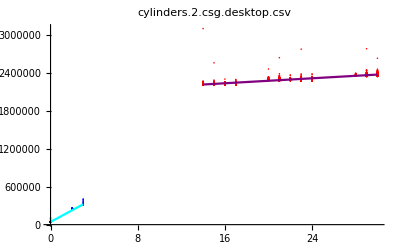
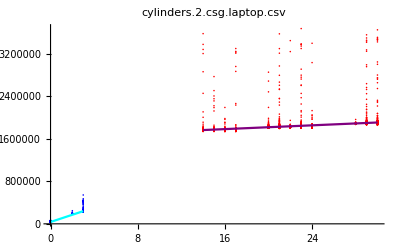
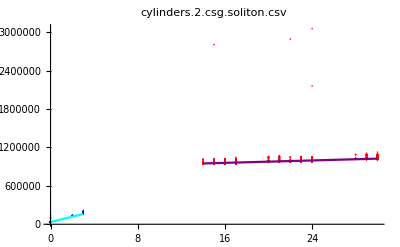
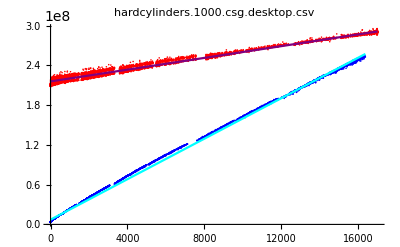
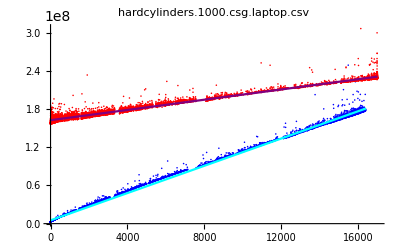
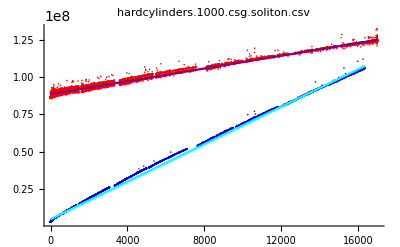
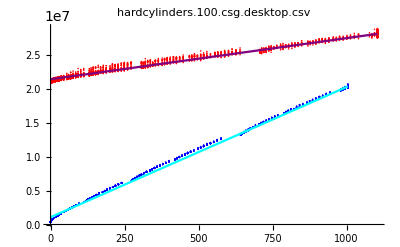
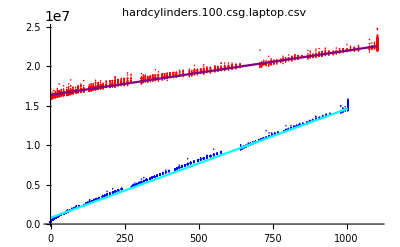
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plots=Map[PlotData, FileNames["*.csv"]]
```

```mathematica
For[i=1, i < Length[plots], i++, plots[[i]]//Print]
```